# Quickchange Primer Design

### Script for generating optimized Quickchange primers. Below are functions needed by the program (DNA->protein translation, reverse complement, Tm score etc.)

```mathematica
translate[codon_]:=Which[codon=="GCT"||codon=="GCC"||codon=="GCA"||codon=="GCG","A",codon=="CGT"||codon=="CGC"||codon=="CGA"||codon=="CGG"||codon=="AGA"||codon=="AGG","R",codon=="AAC"||codon=="AAT","N",codon=="GAT"||codon=="GAC","D",codon=="TGT"||codon=="TGC","C",codon=="CAA"||codon=="CAG","Q",codon=="GAA"||codon=="GAG","E",codon=="GGT"||codon=="GGC"||codon=="GGA"||codon=="GGG","G",codon=="CAT"||codon=="CAC","H",codon=="ATT"||codon=="ATC"||codon=="ATA","I",codon=="TTA"||codon=="TTG"||codon=="CTT"||codon=="CTC"||codon=="CTA"||codon=="CTG","L",codon=="AAA"||codon=="AAG","K",codon=="ATG","M",codon=="TTT"||codon=="TTC","F",codon=="CCT"||codon=="CCC"||codon=="CCA"||codon=="CCG","P",codon=="TCT"||codon=="TCC"||codon=="TCA"||codon=="TCG"||codon=="AGT"||codon=="AGC","S",codon=="ACT"||codon=="ACC"||codon=="ACA"||codon=="ACG","T",codon=="TGG","W",codon=="TAT"||codon=="TAC","Y",codon=="GTT"||codon=="GTC"||codon=="GTA"||codon=="GTG","V"]

getcomplement[base_]:=Which[base=="G","C",base=="C","G",base=="T","A",base=="A","T"]

reversecomplement[sequence_]:=Module[{temp1,complement},

temp1=Characters[sequence];

complement=Table[getcomplement[temp1[[i]]],{i,1,Length[temp1]}];

StringJoin[Reverse[complement]]

]

primerparams[sequence_,annealingportion_,mismatch_]:=Module[{n,g,c,gc},

n=StringLength[sequence];

g=StringCount[sequence,"G"];

c=StringCount[sequence,"C"];

gc=(g+c)/n*100.0;

(*Print[TableForm[{{"Length","%GC","Tm"},{n,gc,81.5+0.41*gc-(675.0/n)-mismatch/42*100.}}]];*)

{n,gc,81.5+0.41*gc-(675.0/n)-mismatch/42*100.}

]

Tmscore[Tm_]:=Piecewise[{{2,Tm≥78.0&&Tm<82.0},{(Tm-77.0)+1,Tm<78.0},{-1*(Tm-82.0)+2,Tm≥82.0}}]

alanine={"GCT","GCC","GCA","GCG"};

arginine={"CGT","CGC","CGA","CGG","AGA","AGG"};

asparagine={"AAC","AAT","TAA"};

aspartate={"GAT","GAC"};

cysteine={"TGT","TGC"};

glutamine={"CAA","CAG"};

glutamate={"GAA","GAG"};

glycine={"GGT","GGC","GGA","GGG"};

histidine={"CAT","CAC"};

isoleucine={"ATT","ATC","ATA"};

leucine={"TTA","TTG","CTT","CTC","CTA","CTG"};

lysine={"AAA","AAG"};

methionine={"ATG"};

phenylalanine={"TTT","TTC"};

proline={"CCT","CCC","CCA","CCG"};

serine={"TCT","TCC","TCA","TCG","AGT","AGC"};

threonine={"ACT","ACC","ACA","ACG"};

tryptophan={"TGG"};

tyrosine={"TAT","TAC"};

valine={"GTT","GTC","GTA","GTG"};
```

### Open an external Python process to calculate hairpin Tms using Primer3:

```mathematica
Tmcounter=0;

pythonpath=StartProcess[{path,"-i"}];

cmd="import primer3";
Pause[0.001];
WriteLine[pythonpath,cmd];

calcHairpin[sequence_]:=(

Tmcounternew=Tmcounter+1;

path="/Library/Frameworks/Python.framework/Versions/2.7/bin/python";

If[Tmcounternew==500,

(KillProcess[pythonpath];

pythonpath=StartProcess[{path,"-i"}];

cmd="import primer3";
Pause[0.001];
WriteLine[pythonpath,cmd];

Tmcounternew=0)];

cmd=StringJoin["primer3.calcHairpin('",sequence,"').tm"];
Pause[0.001];

WriteLine[pythonpath,cmd];

Pause[0.05];

out=ReadString[pythonpath,EndOfBuffer];

Tmcounter=Tmcounternew;

out)
```

### Test if the Tm calculation works (you may need to evaluate the cell above 2x):

```mathematica
calcHairpin["GCACATTCTGTGGGCTTTGGGCAAGCACATAAAATGCC"]
```

58.19360163176441

### Read in DNA sequence of interest, and translate:

```mathematica
pafAsequence="ATGAGCGATAACGATGACATCGAGGTGGAGAGCGACGAAGAGCAACCGAGGTTTCAATCTGCGGCTGACAAACGGGCTCATCATAATGCACTGGAACGAAAACGTAGGGACCACATCAAAGACAGCTTTCACAGTTTGCGGGACTCAGTCCCATCACTCCAAGGAGAGAAGGCATCCCGGGCCCAAATCCTAGACAAAGCCACAGAATATATCCAGTATATGCGAAGGAAAAACCACACACACCAGCAAGATATTGACGACCTCAAGCGGCAGAATGCTCTTCTGGAGCAGCAAGTCCGTGCACTGGAGAAGGCGAGGTCAAGTGCCCAACTGCAGACCAACTACCCCTCCTCAGACAACAGCCTCTACACCAACGCCAAGGGCAGCACCATCTCTGCCTTCGATGGGGGCTCGGACTCCAGCTCGGAGTCTGAGCCTGAAGAGCCCCAAAGCAGGAAGAAGCTCCGGATGGAGGCCAGC";

pafAcodons=Partition[Characters[pafAsequence],3];
```

```mathematica
(* translate *)

translation=Table[{i,StringJoin["Res ",ToString[i*3-2]],StringJoin[pafAcodons[[i]]],Style[translate[StringJoin[pafAcodons[[i]]]],Bold]},{i,1,Length[pafAcodons]}]
```

{{1,Res 1,ATG,M},{2,Res 4,AGC,S},{3,Res 7,GAT,D},{4,Res 10,AAC,N},{5,Res 13,GAT,D},{6,Res 16,GAC,D},{7,Res 19,ATC,I},{8,Res 22,GAG,E},{9,Res 25,GTG,V},{10,Res 28,GAG,E},{11,Res 31,AGC,S},{12,Res 34,GAC,D},{13,Res 37,GAA,E},{14,Res 40,GAG,E},{15,Res 43,CAA,Q},{16,Res 46,CCG,P},{17,Res 49,AGG,R},{18,Res 52,TTT,F},{19,Res 55,CAA,Q},{20,Res 58,TCT,S},{21,Res 61,GCG,A},{22,Res 64,GCT,A},{23,Res 67,GAC,D},{24,Res 70,AAA,K},{25,Res 73,CGG,R},{26,Res 76,GCT,A},{27,Res 79,CAT,H},{28,Res 82,CAT,H},{29,Res 85,AAT,N},{30,Res 88,GCA,A},{31,Res 91,CTG,L},{32,Res 94,GAA,E},{33,Res 97,CGA,R},{34,Res 100,AAA,K},{35,Res 103,CGT,R},{36,Res 106,AGG,R},{37,Res 109,GAC,D},{38,Res 112,CAC,H},{39,Res 115,ATC,I},{40,Res 118,AAA,K},{41,Res 121,GAC,D},{42,Res 124,AGC,S},{43,Res 127,TTT,F},{44,Res 130,CAC,H},{45,Res 133,AGT,S},{46,Res 136,TTG,L},{47,Res 139,CGG,R},{48,Res 142,GAC,D},{49,Res 145,TCA,S},{50,Res 148,GTC,V},{51,Res 151,CCA,P},{52,Res 154,TCA,S},{53,Res 157,CTC,L},{54,Res 160,CAA,Q},{55,Res 163,GGA,G},{56,Res 166,GAG,E},{57,Res 169,AAG,K},{58,Res 172,GCA,A},{59,Res 175,TCC,S},{60,Res 178,CGG,R},{61,Res 181,GCC,A},{62,Res 184,CAA,Q},{63,Res 187,ATC,I},{64,Res 190,CTA,L},{65,Res 193,GAC,D},{66,Res 196,AAA,K},{67,Res 199,GCC,A},{68,Res 202,ACA,T},{69,Res 205,GAA,E},{70,Res 208,TAT,Y},{71,Res 211,ATC,I},{72,Res 214,CAG,Q},{73,Res 217,TAT,Y},{74,Res 220,ATG,M},{75,Res 223,CGA,R},{76,Res 226,AGG,R},{77,Res 229,AAA,K},{78,Res 232,AAC,N},{79,Res 235,CAC,H},{80,Res 238,ACA,T},{81,Res 241,CAC,H},{82,Res 244,CAG,Q},{83,Res 247,CAA,Q},{84,Res 250,GAT,D},{85,Res 253,ATT,I},{86,Res 256,GAC,D},{87,Res 259,GAC,D},{88,Res 262,CTC,L},{89,Res 265,AAG,K},{90,Res 268,CGG,R},{91,Res 271,CAG,Q},{92,Res 274,AAT,N},{93,Res 277,GCT,A},{94,Res 280,CTT,L},{95,Res 283,CTG,L},{96,Res 286,GAG,E},{97,Res 289,CAG,Q},{98,Res 292,CAA,Q},{99,Res 295,GTC,V},{100,Res 298,CGT,R},{101,Res 301,GCA,A},{102,Res 304,CTG,L},{103,Res 307,GAG,E},{104,Res 310,AAG,K},{105,Res 313,GCG,A},{106,Res 316,AGG,R},{107,Res 319,TCA,S},{108,Res 322,AGT,S},{109,Res 325,GCC,A},{110,Res 328,CAA,Q},{111,Res 331,CTG,L},{112,Res 334,CAG,Q},{113,Res 337,ACC,T},{114,Res 340,AAC,N},{115,Res 343,TAC,Y},{116,Res 346,CCC,P},{117,Res 349,TCC,S},{118,Res 352,TCA,S},{119,Res 355,GAC,D},{120,Res 358,AAC,N},{121,Res 361,AGC,S},{122,Res 364,CTC,L},{123,Res 367,TAC,Y},{124,Res 370,ACC,T},{125,Res 373,AAC,N},{126,Res 376,GCC,A},{127,Res 379,AAG,K},{128,Res 382,GGC,G},{129,Res 385,AGC,S},{130,Res 388,ACC,T},{131,Res 391,ATC,I},{132,Res 394,TCT,S},{133,Res 397,GCC,A},{134,Res 400,TTC,F},{135,Res 403,GAT,D},{136,Res 406,GGG,G},{137,Res 409,GGC,G},{138,Res 412,TCG,S},{139,Res 415,GAC,D},{140,Res 418,TCC,S},{141,Res 421,AGC,S},{142,Res 424,TCG,S},{143,Res 427,GAG,E},{144,Res 430,TCT,S},{145,Res 433,GAG,E},{146,Res 436,CCT,P},{147,Res 439,GAA,E},{148,Res 442,GAG,E},{149,Res 445,CCC,P},{150,Res 448,CAA,Q},{151,Res 451,AGC,S},{152,Res 454,AGG,R},{153,Res 457,AAG,K},{154,Res 460,AAG,K},{155,Res 463,CTC,L},{156,Res 466,CGG,R},{157,Res 469,ATG,M},{158,Res 472,GAG,E},{159,Res 475,GCC,A},{160,Res 478,AGC,S}}

### Provide list of subset of mutants with bad hairpin Tms from other notebook:

```mathematica
mutation={"D23A","K24A","R25A","E32A","H38A","S45A","L46A","S49A","I63A","E69A","Q72A","K77A","H38V","S49V","S52V","E56V","Q62V","R47W","V50F","S52G","A21K","R75E","K24S","R25Q"};
```

### Below generates the optimized Quickchange primers, with additional optimization for hairpin Tm:

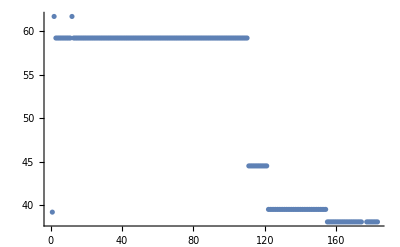

{D23A,{{GTTTCAATCTGCGGCTGCCAAACGGGCTCATCATAATG,{38,50.,81.8559},0.637736,59.2075},{GTTTCAATCTGCGGCTGCCAAACGGGCTCATC,{32,56.25,81.0878},0.637736,59.2075},{CAATCTGCGGCTGCCAAACGGGCTCATC,{28,60.7143,79.9048},0.637736,59.2075}}}

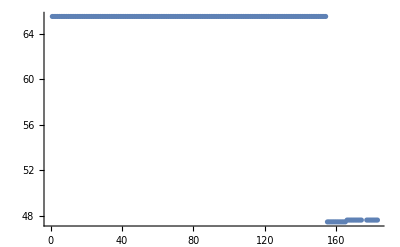

{K24A,{{GTTTCAATCTGCGGCTGACGCACGGGCTCATCATAATG,{38,52.6316,80.5539},-1.24985,65.4995},{CAATCTGCGGCTGACGCACGGGCTCATCATAATGCAC,{37,56.7568,81.7651},-1.24985,65.4995},{CAATCTGCGGCTGACGCACGGGCTCATCATAATG,{34,55.8824,79.7969},-1.24985,65.4995}}}

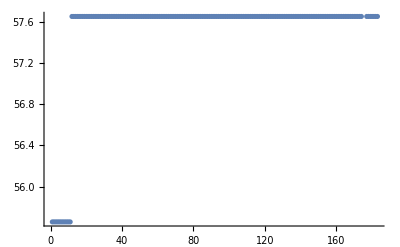

{R25A,{{GCGGCTGACAAAGCGGCTCATCATAATGCAC,{31,54.8387,77.4478},1.15037,55.658},{CAATCTGCGGCTGACAAAGCGGCTCATCATAATGCAC,{37,51.3514,79.5489},1.10484,57.6505},{CTGCGGCTGACAAAGCGGCTCATCATAATGCACTG,{35,54.2857,79.7095},1.10484,57.6505}}}

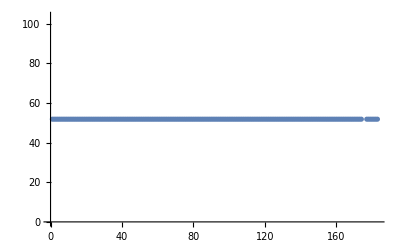

{E32A,{{GCTCATCATAATGCACTGGCACGAAAACGTAGGGAC,{36,50.,80.869},2.85653,51.8116},{CTCATCATAATGCACTGGCACGAAAACGTAGGGACCAC,{38,50.,81.8559},2.85653,51.8116},{CTCATCATAATGCACTGGCACGAAAACGTAGGGAC,{35,48.5714,79.7476},2.85653,51.8116}}}

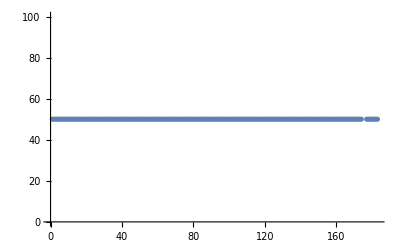

{H38A,{{GAACGAAAACGTAGGGACGCCATCAAAGACAGCTTTC,{37,48.6486,78.4408},3.39616,50.0128},{CGAAAACGTAGGGACGCCATCAAAGACAGCTTTCACAG,{38,50.,79.4749},3.39616,50.0128},{CGAAAACGTAGGGACGCCATCAAAGACAGCTTTCAC,{36,50.,78.4881},3.39616,50.0128}}}

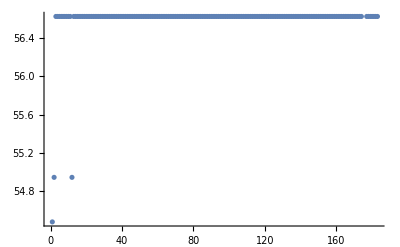

{S45A,{{CATCAAAGACAGCTTTCACGCTTTGCGGGACTCAGTC,{37,51.3514,79.5489},1.41194,56.6269},{CAAAGACAGCTTTCACGCTTTGCGGGACTCAGTC,{34,52.9412,78.591},1.41194,56.6269},{CATCAAAGACAGCTTTCACGCTTTGCGGGACTCAGTCC,{38,52.6316,80.5539},1.16194,56.6269}}}

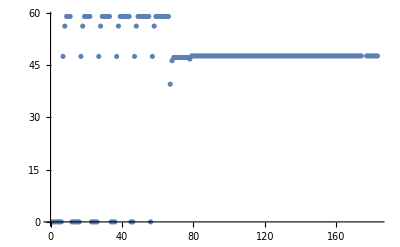

{L46A,{{GACAGCTTTCACAGTGCGCGGGACTCAGTC,{30,60.,78.8381},4.,0.},{CAAAGACAGCTTTCACAGTGCGCGGGACTCAGTCCC,{36,58.3333,81.9048},3.75,46.743},{GACAGCTTTCACAGTGCGCGGGACTCAGTCC,{31,61.2903,80.0929},3.75,47.4895}}}

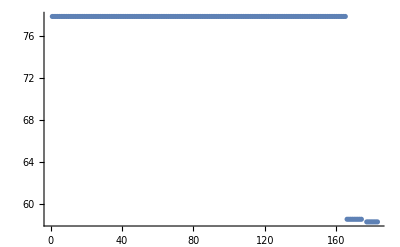

{S49A,{{CACAGTTTGCGGGACGCAGTCCCATCACTC,{30,60.,81.219},-4.94823,77.8274},{CACAGTTTGCGGGACGCAGTCCCATCAC,{28,60.7143,79.9048},-4.94823,77.8274},{CAGTTTGCGGGACGCAGTCCCATCACTC,{28,60.7143,79.9048},-4.94823,77.8274}}}

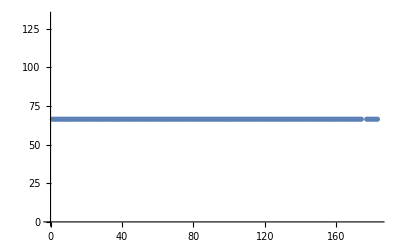

{I63A,{{GCATCCCGGGCCCAAGCCCTAGACAAAG,{28,64.2857,78.9881},-1.55537,66.5179},{CATCCCGGGCCCAAGCCCTAGACAAAGCCAC,{31,64.5161,81.4155},-1.55537,66.5179},{GCATCCCGGGCCCAAGCCCTAGACAAAGCC,{30,66.6667,81.5714},-1.80537,66.5179}}}

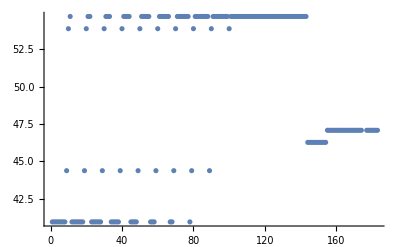

{E69A,{{CTAGACAAAGCCACAGCATATATCCAGTATATGCGAAG,{38,42.1053,78.619},1.99835,54.6722},{CAAATCCTAGACAAAGCCACAGCATATATCCAGTATATGC,{40,40.,78.644},1.99329,53.8557},{CCTAGACAAAGCCACAGCATATATCCAGTATATG,{34,41.1765,76.1485},1.89846,44.3878}}}

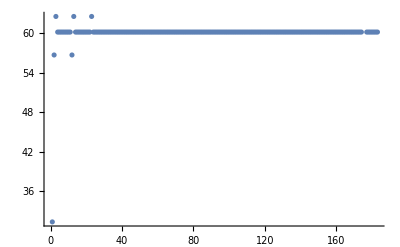

{Q72A,{{CAAAGCCACAGAATATATCGCGTATATGCGAAGGAAAAACCAC,{43,41.8605,78.2032},0.342286,60.1924},{CTAGACAAAGCCACAGAATATATCGCGTATATGCGAAGGAAAAACC,{46,41.3043,78.999},0.0922856,60.1924},{GACAAAGCCACAGAATATATCGCGTATATGCGAAGGAAAAACC,{43,41.8605,78.2032},0.0922856,60.1924}}}

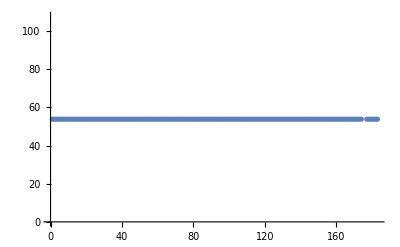

{K77A,{{CAGTATATGCGAAGGGCAAACCACACACACCAGCAAG,{37,51.3514,79.5489},2.25681,53.8106},{CCAGTATATGCGAAGGGCAAACCACACACACCAGCAAG,{38,52.6316,80.5539},2.00681,53.8106},{CCAGTATATGCGAAGGGCAAACCACACACACCAG,{34,52.9412,78.591},2.00681,53.8106}}}

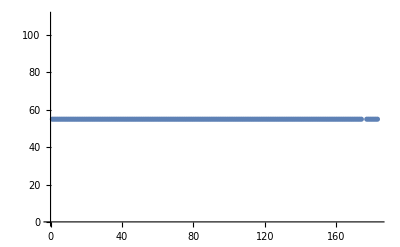

{H38V,{{GAACGAAAACGTAGGGACGTCATCAAAGACAGCTTTCAC,{39,46.1538,78.3535},1.90973,54.9676},{CGAAAACGTAGGGACGTCATCAAAGACAGCTTTCACAG,{38,47.3684,78.396},1.90973,54.9676},{GGAACGAAAACGTAGGGACGTCATCAAAGACAGCTTTC,{38,47.3684,78.396},1.65973,54.9676}}}

-Graphics-

{S49V,{{CTTTCACAGTTTGCGGGACGTAGTCCCATCACTCCAAG,{38,52.6316,80.5539},-4.94823,77.8274},{CACAGTTTGCGGGACGTAGTCCCATCACTCCAAGGAG,{37,56.7568,81.7651},-4.94823,77.8274},{CACAGTTTGCGGGACGTAGTCCCATCACTCCAAG,{34,55.8824,79.7969},-4.94823,77.8274}}}

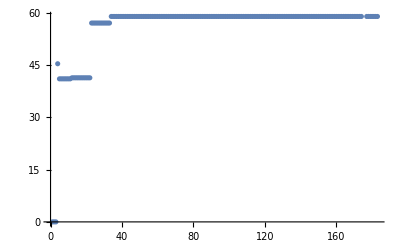

{S52V,{{GACTCAGTCCCAGTACTCCAAGGAGAGAAGGC,{32,56.25,78.7068},3.75,41.0522},{GGACTCAGTCCCAGTACTCCAAGGAGAGAAGGC,{33,57.5758,79.8896},3.5,41.3471},{GGACTCAGTCCCAGTACTCCAAGGAGAGAAGG,{32,56.25,78.7068},3.5,41.3471}}}

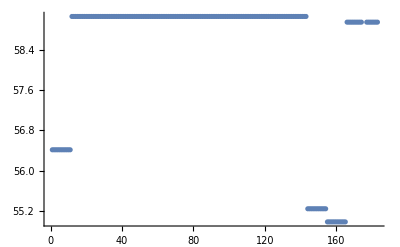

{E56V,{{CATCACTCCAAGGAGTGAAGGCATCCCGGG,{30,60.,81.219},0.428677,59.0711},{CATCACTCCAAGGAGTGAAGGCATCCCGG,{29,58.6207,79.8777},0.428677,59.0711},{CATCACTCCAAGGAGTGAAGGCATCCCG,{28,57.1429,78.4405},0.428677,59.0711}}}

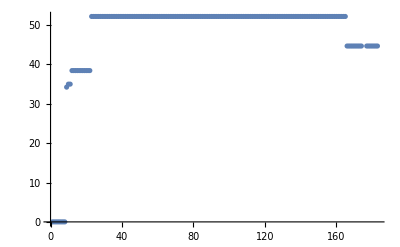

{Q62V,{{GCATCCCGGGCCGTAATCCTAGACAAAGCCAC,{32,59.375,79.9881},4.,34.9897},{GGCATCCCGGGCCGTAATCCTAGACAAAGCCAC,{33,60.6061,81.132},3.75,38.4308},{GCATCCCGGGCCGTAATCCTAGACAAAGCC,{30,60.,78.8381},3.75,34.2228}}}

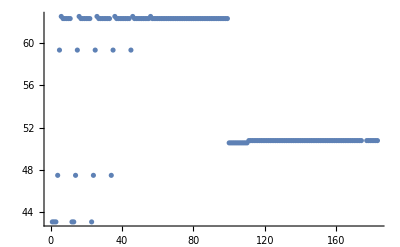

{R47W,{{GCTTTCACAGTTTGTGGGACTCAGTCC,{27,51.8519,75.3783},1.12831,47.4895},{AAAGACAGCTTTCACAGTTTGTGGGACTCAGTCCCATCAC,{40,47.5,81.719},0.382393,50.5587},{CAGCTTTCACAGTTTGTGGGACTCAGTCCC,{30,53.3333,78.4857},0.349717,59.3343}}}

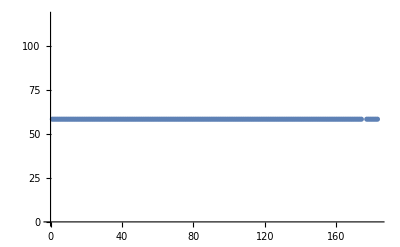

{V50F,{{CACAGTTTGCGGGACTCATTCCCATCACTCCAAG,{34,52.9412,80.972},0.880372,58.3988},{CAGTTTGCGGGACTCATTCCCATCACTCCAAG,{32,53.125,79.8065},0.880372,58.3988},{GTTTGCGGGACTCATTCCCATCACTCCAAGGAG,{33,54.5455,81.0281},0.880372,58.3988}}}

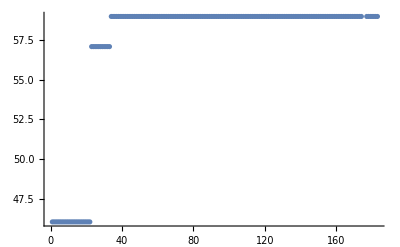

{S52G,{{GGACTCAGTCCCAGGACTCCAAGGAGAGAAG,{31,58.0645,78.7704},3.75,46.0785},{GACTCAGTCCCAGGACTCCAAGGAGAGAAGGC,{32,59.375,79.9881},3.75,46.0785},{GACTCAGTCCCAGGACTCCAAGGAGAGAAGG,{31,58.0645,78.7704},3.75,46.0785}}}

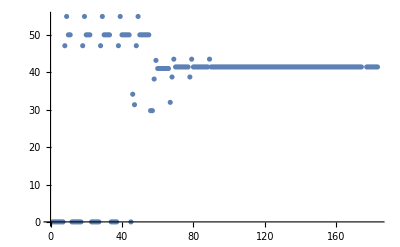

{A21K,{{GCAACCGAGGTTTCAATCTAAGGCTGACAAACGGGCTC,{38,52.6316,80.5539},4.,41.4455},{CAACCGAGGTTTCAATCTAAGGCTGACAAACGGGCTC,{37,51.3514,79.5489},4.,41.4455},{CAACCGAGGTTTCAATCTAAGGCTGACAAACGGGC,{35,51.4286,78.5381},3.75,38.7592}}}

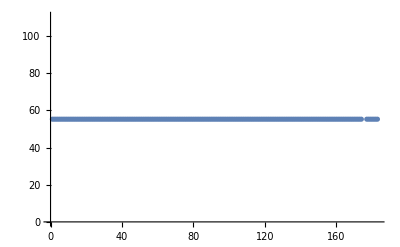

{R75E,{{CACAGAATATATCCAGTATATGGAAAGGAAAAACCACACACACCAG,{46,39.1304,78.1077},1.80301,55.3233},{CAGAATATATCCAGTATATGGAAAGGAAAAACCACACACACCAGCAAG,{48,39.5833,78.9048},1.80301,55.3233},{GCCACAGAATATATCCAGTATATGGAAAGGAAAAACCACACACACC,{46,41.3043,78.999},1.55301,55.3233}}}

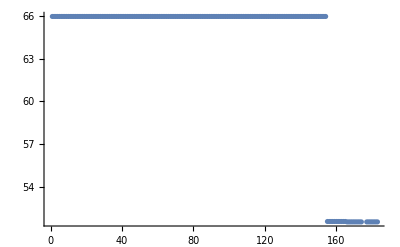

{K24S,{{GTTTCAATCTGCGGCTGACAGCCGGGCTCATCATAATG,{38,52.6316,80.5539},-1.39868,65.9956},{CAATCTGCGGCTGACAGCCGGGCTCATCATAATGCAC,{37,56.7568,81.7651},-1.39868,65.9956},{CAATCTGCGGCTGACAGCCGGGCTCATCATAATG,{34,55.8824,79.7969},-1.39868,65.9956}}}

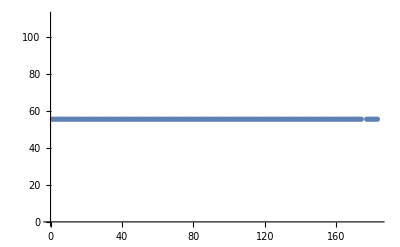

{R25Q,{{CAATCTGCGGCTGACAAACAGGCTCATCATAATGCAC,{37,48.6486,80.8218},1.77314,55.4229},{CAATCTGCGGCTGACAAACAGGCTCATCATAATG,{34,47.0588,78.5602},1.77314,55.4229},{CTGCGGCTGACAAACAGGCTCATCATAATGCACTG,{35,51.4286,80.919},1.77314,55.4229}}}

```mathematica
Dynamic[loop]
Dynamic[i]

Do[

resnumber=ToExpression[StringDrop[StringDrop[mutation[[loop]],{1}],{-1}]];

restypeIN=StringTake[mutation[[loop]],{-1}];

(* calculate the number of base pair changes between the wild-type sequence and all codons of the mutated amino acid *)
newrescodons=Which[restypeIN=="A",alanine,restypeIN=="G",glycine,restypeIN=="D",aspartate,restypeIN=="N",asparagine,restypeIN=="E",glutamate,restypeIN=="Q",glutamine,restypeIN=="V",valine,restypeIN=="L",leucine,restypeIN=="I",isoleucine,restypeIN=="P",proline,restypeIN=="H",histidine,restypeIN=="K",lysine,restypeIN=="R",arginine,restypeIN=="Y",tyrosine,restypeIN=="F",phenylalanine,restypeIN=="W",tryptophan,restypeIN=="S",serine,restypeIN=="T",threonine,restypeIN=="C",cysteine,restypeIN=="M",methionine];

testwt=pafAcodons[[resnumber]];
(*Print[testwt];

Print[translation[[resnumber]]];*)

Do[

testmutant=Characters[newrescodons[[i]]];

codondiff[i]=If[testwt[[1]]==testmutant[[1]],0,1]+If[testwt[[2]]==testmutant[[2]],0,1]+If[testwt[[3]]==testmutant[[3]],0,1];

,{i,1,Length[newrescodons]}];

(* select codon requiring the least number of base pair changes *)
newcodon=Sort[Table[{StringJoin[newrescodons[[i]]],codondiff[i]},{i,1,Length[newrescodons]}],#1[[2]]<#2[[2]]&][[1]];

(*Print["New codon"];
Print[newcodon];*)

(* test a range of flanking lengths *)
base5prime=resnumber*3-2;
base3prime=resnumber*3;

(* below plots the piecewise function used by Tmscore *)
(* Plot[Piecewise[{{2,Tm≥78.0},{(Tm-77.0)+1,Tm≥77.0},{(Tm-70.0)*0.142857,Tm<77.0}}],{Tm,70,85}] *)

(* counter for indexing the mutagenic primers *)
counter=0;

Do[

Do[

fiveprimeend=base5prime-i;
threeprimeend=base3prime+j;

wildtypeprimer=StringTake[pafAsequence,{fiveprimeend,threeprimeend}];

(* insert mutation into sense primer *)
mutagenicprimer=StringJoin[StringTake[pafAsequence,{fiveprimeend,base5prime-1}],StringJoin[newcodon[[1]]],StringTake[pafAsequence,{base3prime+1,threeprimeend}]];

gcfirst=If[StringTake[mutagenicprimer,1]=="G"||StringTake[mutagenicprimer,1]=="C",1,0];

gclast=If[StringTake[mutagenicprimer,-1]=="G"||StringTake[mutagenicprimer,-1]=="C",1,0];

(* calculate the annealing portion of the sequence for Tm calcuations *)
wtseq=Characters[wildtypeprimer];
mutantseq=Characters[mutagenicprimer];

seqforTm=StringJoin[Select[Table[If[wtseq[[i]]==mutantseq[[i]],wtseq[[i]]],{i,1,Length[wtseq]}],#=="G"||#=="C"||#=="A"||#=="T"&]];

(* use "primerparams" function to calculate %GC and melting temperature *)
parameters=primerparams[mutagenicprimer,seqforTm,newcodon[[2]]];

(* include penalties for primer 3' self-complementarity *)
onebase=If[getcomplement[StringTake[mutagenicprimer,-1]]==StringTake[mutagenicprimer,{-2}],-0.25,0];
twobases=If[getcomplement[StringTake[mutagenicprimer,{2}]]==StringTake[mutagenicprimer,{-2}]&&onebase==-0.25,-0.5,0];
threebases=If[getcomplement[StringTake[mutagenicprimer,{3}]]==StringTake[mutagenicprimer,{-3}]&&twobases==-0.25,-1.0,0];

(* hairpin penalty function *)
hairpin=Piecewise[{{0,hTm<48.0},{-0.3*hTm+0.3*48.0,hTm≥48.0}}];

hairpinTm=ToExpression[calcHairpin[mutagenicprimer]];

(* calculate final "objective function" score *)
(* 06/24/26 - included a penalty for longer primers (to reduce oligo synthesis costs) *)
endscore=gcfirst+gclast+Tmscore[parameters[[3]]]+If[StringLength[mutagenicprimer]>19*2&&parameters[[3]]>79.0,(-0.04*StringLength[mutagenicprimer]),0]+If[StringTake[mutagenicprimer,{-1}]==StringTake[mutagenicprimer,{-2}],-0.25,0.0]+If[StringTake[mutagenicprimer,{1}]==StringTake[mutagenicprimer,{2}],-0.25,0.0]+onebase+twobases+threebases+(hairpin/.{hTm->hairpinTm});

(* need to clear the self-complementarity tests otherwise will be included in calculations for subsequent primers *)
Clear[onebase,twobases,threebases];

(* counter *)
counter2=counter+1;
counter=counter2;

primertest[counter]={mutagenicprimer,parameters,endscore,hairpinTm};

,{j,i-5,i+5}]

,{i,12,28}];

allprimers=Table[primertest[m],{m,1,counter}];

(*Print[allprimers];*)

Print[ListPlot[allprimers[[All,4]],PlotRange->All]];

best[mutation[[loop]]]={mutation[[loop]],Select[Sort[allprimers,#1[[3]]>#2[[3]]&],#[[2,1]]<50&][[1;;3]]};

Print[best[mutation[[loop]]]];

,{loop,1,Length[mutation]}]
```

### Write out list of top “hit” for each mutant, and calculate hairpin Tm for all:

```mathematica
mutationproperresnums=Table[StringJoin[StringTake[mutation[[n]],1],ToString[ToExpression[StringDrop[StringDrop[mutation[[n]],-1],1]]],StringTake[mutation[[n]],-1]],{n,1,Length[mutation]}];

Dynamic[n]

primers=Table[{ToExpression[StringDrop[StringDrop[mutation[[n]],-1],1]],mutationproperresnums[[n]],best[mutation[[n]]][[2,1,1]],"","","","","",reversecomplement[best[mutation[[n]]][[2,1,1]]],ToExpression[calcHairpin[best[mutation[[n]]][[2,1,1]]]]},{n,1,Length[mutation]}]
```

{{23,D23A,GTTTCAATCTGCGGCTGCCAAACGGGCTCATCATAATG,,,,,,CATTATGATGAGCCCGTTTGGCAGCCGCAGATTGAAAC,59.2075},{24,K24A,GTTTCAATCTGCGGCTGACGCACGGGCTCATCATAATG,,,,,,CATTATGATGAGCCCGTGCGTCAGCCGCAGATTGAAAC,65.4995},{25,R25A,GCGGCTGACAAAGCGGCTCATCATAATGCAC,,,,,,GTGCATTATGATGAGCCGCTTTGTCAGCCGC,55.658},{32,E32A,GCTCATCATAATGCACTGGCACGAAAACGTAGGGAC,,,,,,GTCCCTACGTTTTCGTGCCAGTGCATTATGATGAGC,51.8116},{38,H38A,GAACGAAAACGTAGGGACGCCATCAAAGACAGCTTTC,,,,,,GAAAGCTGTCTTTGATGGCGTCCCTACGTTTTCGTTC,50.0128},{45,S45A,CATCAAAGACAGCTTTCACGCTTTGCGGGACTCAGTC,,,,,,GACTGAGTCCCGCAAAGCGTGAAAGCTGTCTTTGATG,56.6269},{46,L46A,GACAGCTTTCACAGTGCGCGGGACTCAGTC,,,,,,GACTGAGTCCCGCGCACTGTGAAAGCTGTC,0.},{49,S49A,CACAGTTTGCGGGACGCAGTCCCATCACTC,,,,,,GAGTGATGGGACTGCGTCCCGCAAACTGTG,77.8274},{63,I63A,GCATCCCGGGCCCAAGCCCTAGACAAAG,,,,,,CTTTGTCTAGGGCTTGGGCCCGGGATGC,66.5179},{69,E69A,CTAGACAAAGCCACAGCATATATCCAGTATATGCGAAG,,,,,,CTTCGCATATACTGGATATATGCTGTGGCTTTGTCTAG,54.6722},{72,Q72A,CAAAGCCACAGAATATATCGCGTATATGCGAAGGAAAAACCAC,,,,,,GTGGTTTTTCCTTCGCATATACGCGATATATTCTGTGGCTTTG,60.1924},{77,K77A,CAGTATATGCGAAGGGCAAACCACACACACCAGCAAG,,,,,,CTTGCTGGTGTGTGTGGTTTGCCCTTCGCATATACTG,53.8106},{38,H38V,GAACGAAAACGTAGGGACGTCATCAAAGACAGCTTTCAC,,,,,,GTGAAAGCTGTCTTTGATGACGTCCCTACGTTTTCGTTC,54.9676},{49,S49V,CTTTCACAGTTTGCGGGACGTAGTCCCATCACTCCAAG,,,,,,CTTGGAGTGATGGGACTACGTCCCGCAAACTGTGAAAG,77.8274},{52,S52V,GACTCAGTCCCAGTACTCCAAGGAGAGAAGGC,,,,,,GCCTTCTCTCCTTGGAGTACTGGGACTGAGTC,41.0522},{56,E56V,CATCACTCCAAGGAGTGAAGGCATCCCGGG,,,,,,CCCGGGATGCCTTCACTCCTTGGAGTGATG,59.0711},{62,Q62V,GCATCCCGGGCCGTAATCCTAGACAAAGCCAC,,,,,,GTGGCTTTGTCTAGGATTACGGCCCGGGATGC,34.9897},{47,R47W,GCTTTCACAGTTTGTGGGACTCAGTCC,,,,,,GGACTGAGTCCCACAAACTGTGAAAGC,47.4895},{50,V50F,CACAGTTTGCGGGACTCATTCCCATCACTCCAAG,,,,,,CTTGGAGTGATGGGAATGAGTCCCGCAAACTGTG,58.3988},{52,S52G,GGACTCAGTCCCAGGACTCCAAGGAGAGAAG,,,,,,CTTCTCTCCTTGGAGTCCTGGGACTGAGTCC,46.0785},{21,A21K,GCAACCGAGGTTTCAATCTAAGGCTGACAAACGGGCTC,,,,,,GAGCCCGTTTGTCAGCCTTAGATTGAAACCTCGGTTGC,41.4455},{75,R75E,CACAGAATATATCCAGTATATGGAAAGGAAAAACCACACACACCAG,,,,,,CTGGTGTGTGTGGTTTTTCCTTTCCATATACTGGATATATTCTGTG,55.3233},{24,K24S,GTTTCAATCTGCGGCTGACAGCCGGGCTCATCATAATG,,,,,,CATTATGATGAGCCCGGCTGTCAGCCGCAGATTGAAAC,65.9956},{25,R25Q,CAATCTGCGGCTGACAAACAGGCTCATCATAATGCAC,,,,,,GTGCATTATGATGAGCCTGTTTGTCAGCCGCAGATTG,55.4229}}

```mathematica
Export["/Users/craig/Dropbox/craig_analysis_and_simulation_code/MAX_mutagenesis/BAD_hairpin_Tm_primers.csv",primers]
```

/Users/craig/Dropbox/craig_analysis_and_simulation_code/MAX_mutagenesis/BAD_hairpin_Tm_primers.csv